# CASO 1

## Parte primera

1. Desarrollar un sistema generador de números aleatorios basado en un generador lineal congruencial mixto que siga una distribución uniforme entre[0, 1].

```mathematica
<< "D:\Users\jontx\Dropbox\Clase\2 Master\RRT\Caso 1\RandomData.m"
```

El siguiente comando permite ver cuales son las funciones que incluye el fichero RandomData.m

```mathematica
?RandomData`*
```

La librería que nos proporciona Armando dispone de una función RandomData que no es mas que un generador de números aleatorios que sigue una distribución uniforme entre 0 y 1.

2. Probar el generador y demostrar mediante un histograma la bondad del generador.

```mathematica
muestras=10000;
```

```mathematica
listaUni=Table[RandomData[], {i, muestras}];
```

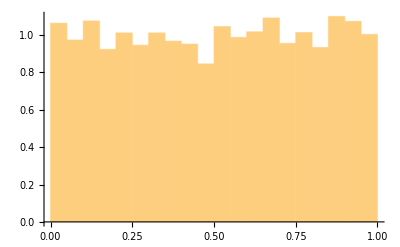

```mathematica
Histogram[listaUni, 20, "PDF"]
```

Disponer de una distribución uniforme entre 0 y 1 quiere decir que todos los valores generados son igual de probables, y que la función de densidad de probabilidad del generador debe ser constante en el intervalo [0,1] con valor 1/(1-0)=1 y 0 en el resto de intervalos. Como vemos, el resultado obtenido con el generador que nos proporciona la librería RandomData.m se aproxima bastante a esta definición teórica.

3. Implementar el método de transformada inversa para obtener una distribución aleatoria exponencial de tiempo entre llegadas 1/λ.Representar en un histograma los valores obtenidos.

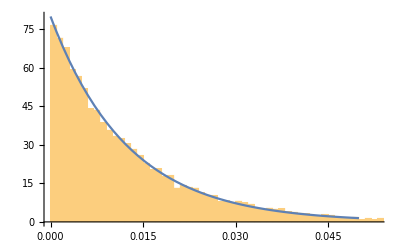

```mathematica
mu=100;
lamda=80;
ro=lamda/mu;
listaExp=Table[RandomExp[lamda],{i,muestras}];
(*Histogram[listaExp, 100, "PDF"]*)
Show[Histogram[listaExp, 100, "PDF"], Plot[lamda*Exp[-lamda*t],{t,0,0.05}]]
```

```mathematica
Mean[listaExp]
1/lamda//N
```

0.0125316

0.0125

Como vemos, la función de densidad de probabilidad obtenida a partir de los valores generados mediante la función RandomExp se acerca bastante a la función de densidad de probabilidad de una distribución exponencial. Así mismo, mencionar que la media de los valores obtenidos se aproxima a 1/λ, que era lo que se esperaba conseguir.

Destacar que cuantos más valores se utilicen para calcular la densidad de probabilidad de cada una de las distribuciones, el resultado más se parecerá al teórico.

## Parte segunda

4. Desarrollar un simulador de una cola M/M/1 con tasa λ de llegadas y μ de servicio.Representar en un diagrama que evolucione en el tiempo el número de usuarios en el sistema

```mathematica
mu=100;
lamda=80;
ro=lamda/mu;
muestras=10000;
InterArrivalsTime=Table[RandomExp[lamda],muestras];
```

Las llegadas de la cola M/M/1 forman un proceso poissoniano. Es decir, las llegadas forman un proceso estocástico cuya particularidad es que el tiempo entre llegadas es independiente del resto de tiempos entre llegadas, y además, estos siguen una distribución exponencial. Por tanto, al generar valores aleatorios mediante la función RandomExp lo que realmente estamos generando no es más que una lista que contiene la diferencia de tiempos entre una llegada y la anterior. Para conseguir los tiempos de llegada absolutos, que realmente es lo que nos interesa, se han de sumar en cada instante de tiempo todos los tiempos entre llegadas hasta ese momento.

```mathematica
ArrivalsTime=Accumulate[InterArrivalsTime];
```

```mathematica
ServTime=Table[RandomExp[mu], muestras];
```

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,arrivals]]
```

La función FifoSchedulling permite calcular el tiempo en el que salen cada uno de los paquetes. A la función se le pasan los tiempos de llegada de los paquetes y el tiempo que tardan en servirse. Después, a través de la variable checkTime se va calculando el tiempo en el que sale cada uno de los paquetes. En cada iteración se compara si la cola esta libre o no. Si la cola se encontraba libre, la variable checkTime toma el valor de la suma del instante en el que se ha dado la llegada y el tiempo que se tarda en servir dicha llegada. Por el contrario, si se encontraba ocupada, el paquete de la iteración en la que nos encontramos se comenzará a servir tras acabar de servir el que ya se encontraba en la cola. Es decir, el paquete saldrá en el instante checkTime+tiempo de servir la nueva llegada.

```mathematica
Departu=FifoSchedulling[ArrivalsTime, ServTime];
```

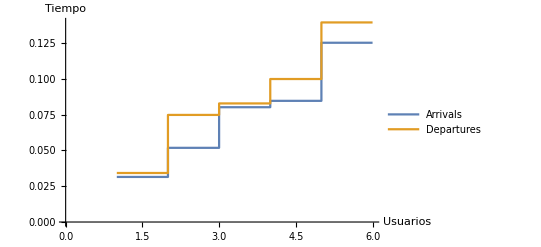

```mathematica
ListStepPlot[{ArrivalsTime[[1;;5]], Departu[[1;;5]]}, AxesLabel->{Usuarios, Tiempo}, PlotLegends->{"Arrivals","Departures"}]
```

Tal y como se puede observar, la grafica anterior tiene los usuarios en el eje x y el tiempo en el eje y, sin embargo, a nosotros nos interesa mostrarlos al revés.Para darle la vuelta, creamos una función que coja el array de tiempos y con cada uno de los elementos genere una lista de dos elementos, {tiempo, usuarios en ese instante}.

```mathematica
PointStair[array_]:= 
Module[{n=0},
Map[{#,n++}&,array]];
```

Las siguientes dos graficas muestran, a lo largo del tiempo, los eventos que se van dando tanto en las llegadas como en las salidas.Tal y como veremos a continuación, cruzando la información de las dos líneas representadas en las graficas se puede obtener el tiempo de espera que ha sufrido cada uno de los usuarios en el sistema. Concretamente, dicho tiempo de espera no es más que la diferencia de tiempos que existe entre cada una de las paralelas que se observan en las gráficas.

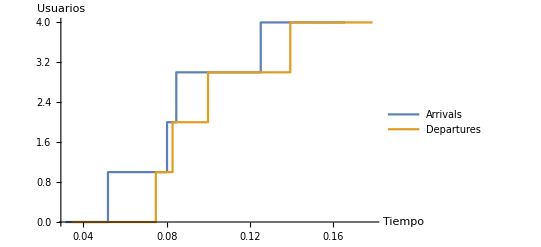

```mathematica
ListStepPlot[{PointStair[ArrivalsTime][[1;;5]], PointStair[Departu][[1;;5]]}, AxesLabel->{Tiempo, Usuarios}, PlotLegends->{"Arrivals","Departures"}]
```

```mathematica
Manipulate[ListStepPlot[{PointStair[ArrivalsTime][[origin;;origin+width]],PointStair[Departu][[origin;;origin+width]]}, AxesLabel->{Tiempo, Usuarios}, PlotLegends->{"Arrivals","Departures"}],{origin,1,1000-width,1},{width,10,If[muestras-origin> 0, muestras-origin, 10],1}]
```

```mathematica
CreateEventList[list_, value_]:=Map[{#,value} &, list];
```

```mathematica
NumUsers[list_]:= Module[{n=0,lastTime=0},Flatten[Map[{{lastTime,n},{lastTime=#[[1]],If[#[[2]]==1,n++,n--]}}&,list],1]]
```

```mathematica
ArrivalsEvent=CreateEventList[ArrivalsTime, 1];
DepartureEvent=CreateEventList[Departu, -1];
ListaEventos=Sort[Join[ArrivalsEvent, DepartureEvent]];
usuarios=NumUsers[ListaEventos];
```

Esta grafica muestra la evolución en el tiempo de los usuarios del sistema.Como vemos, con los parámetros establecidos, en un mismo instante de tiempos hemos llegado a tener un número máximo de 18 usuarios.

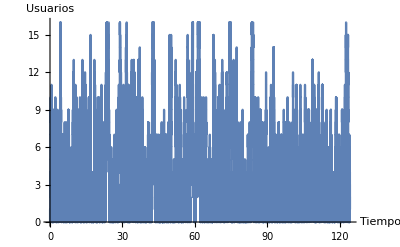

```mathematica
ListLinePlot[usuarios, AxesLabel->{Tiempo, Usuarios}]
```

```mathematica
Manipulate[ListLinePlot[usuarios[[origin;;origin+width]],AxesLabel->{Tiempo, Usuarios}],{origin,1,Length[usuarios]-width,1},{width,10,If[Length[usuarios]-origin> 0, Length[usuarios]-origin, 10],1}]
```

5.Representar el tiempo medio de espera en el sistema normalizado por μ para diferentes valores de ρ. Hacerlo con la curva teórica y representar los puntos obtenidos en las simulaciones.

```mathematica
curvaTeorica=Plot[1/(1-ro), {ro,0,1}, AxesOrigin->{0,0}, AxesLabel->{Ro, muEt[t]}, PlotLegends->{"Teorica"}];
```

```mathematica
GetTiempoMedio[]:=
Module[{mu, lamda, ro, arrivals, services,departures, meanTime,nmuestras},

	mu=100;
	nmuestras=10000;
	lamda=Table[i,{i,1,mu}];
	Map[
(
ro=#/mu//N;
arrivals=Accumulate[Table[RandomExp[#],nmuestras]];
services=Table[RandomExp[mu],nmuestras];
departures=FifoSchedulling[arrivals, services];
meanTime=Mean[departures-arrivals];
{ro, meanTime*mu}
)
&,lamda]
]
```

```mathematica
curvaPractica=ListPlot[GetTiempoMedio[], {AxesLabel->{Ro, muEt[t]}, PlotLegends->{"Practica"}, PlotStyle->Red}];
```

El tiempo medio de espera simulado se calcula como la media de la diferencia de tiempos en cada instante de las salidas y las llegadas.Tal y como ocurría en casos anteriores, cuantas más muestras se utilicen el valor simulado se aproxima más al teórico.En mi caso, he utilizado un total de 10000 muestras con las cuales he conseguido una aproximación bastante precisa.

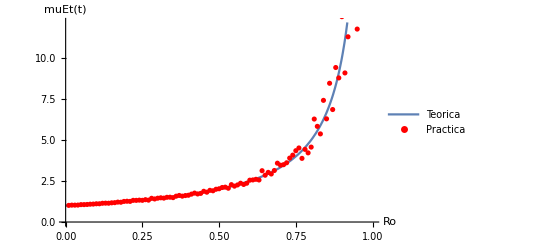

```mathematica
Show[curvaTeorica, curvaPractica]
```

## Parte tercera

6.Representar las probabilidades de estado pn de la cola M/M/1 teóricas, así como las obtenidas por simulación para diferentes puntos de ensayo.Comprobar si esa distribución coincide con la visualizada según la propiedad PASTA en los tiempos de llegada.

La probabilidad simulada de cada estado se calcula como el tiempo total que el sistema ha estado en dicho estado, divido entre el tiempo total. Por el contrario, si deseamos calcular dichas probabilidades haciendo uso de la propiedad PASTA únicamente habría que tener en cuenta los casos en los que se da un incremento de usuarios en el sistema, y el número de veces que se ha dado dicha situación.

Dicho de otra manera, para calcular la probabilidad de cada estado mediante PASTA, se ha de tener un contador por estado el cual se incremente cada vez que dicho estado pasa a un estado que indique una mayor cantidad de usuarios, y un contador general que cuente cada vez que se incremente uno de los contadores de estado. Hecho esto, bastaría con dividir cada uno de los contadores de estado entre el valor del contador general.

Por último, las probabilidades de estado teóricas se calculan como (1 - ro)*(ro^n) donde n es el estado del cual se desea calcular la probabilidad y ro es lamda/mu.

```mathematica
ProbEstadoPrac[usuario_]:=
Module[ {arrayTmp, arrayEstados, maxEstados},
maxEstados=Max[Map[(#[[2]]) &,usuario]]+1;
arrayEstados=Table[0,maxEstados];
arrayTmp=Partition[usuario,2];
Map[(arrayEstados[[(# [[1]][[2]]+1)]]+=(#[[2]][[1]]-#[[1]][[1]]))&, arrayTmp];
Return[arrayEstados/usuario[[-1]][[1]]]
]
```

```mathematica
ProbEstadoPasta[usuario_]:=
Module[ {arrayTmp, arrayEstados, maxEstados, valorAnterior, contadorEstados},
maxEstados=Max[Map[(#[[2]]) &,usuario]]+1;
contadorEstados=0;
arrayEstados=Table[0,maxEstados];
arrayTmp=Partition[usuario,2];
valorAnterior=usuario[[1]][[2]];
Map[(
If[#[[1]][[2]]> valorAnterior,
(arrayEstados[[valorAnterior+1]]+=1; 
valorAnterior=#[[1]][[2]];
 contadorEstados+=1;)
, valorAnterior=#[[1]][[2]]]
	)&, arrayTmp];
Return[arrayEstados/contadorEstados]
]
```

```mathematica
ProbEstadoTeorico[lamda_, mu_, nestados_]:=
Module[{array,ro0},
ro0=lamda/mu;
array=Table[i,{i,0,nestados}];
Map[
(
(1-ro0)*(ro0^#)
)

&, array]
]
```

```mathematica
probPractica=ProbEstadoPrac[usuarios];
```

```mathematica
probPasta=N [ProbEstadoPasta[usuarios]];
```

```mathematica
probTeorica=N[ProbEstadoTeorico[lamda, mu, Length[probPractica]]];
```

En la siguiente grafica se puede observar cómo tanto la distribución obtenida mediante la propiedad PASTA como la obtenida mediante los valores de la simulación se asemejan bastante a la distribución teórica.

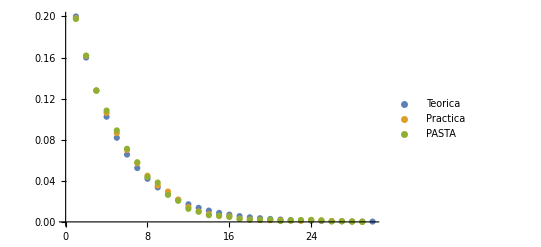

```mathematica
ListPlot[{probTeorica, probPractica, probPasta}, PlotLegends->{"Teorica","Practica", "PASTA"}]
```

## Parte cuarta

7. Preparar las gráficas de rendimiento de colas vistas en Teoría de la información para los casos específicos que se elijan. Revisar la teoría.

En este último apartado he optado por simular una cola M/M/2 formada por un servidor con tasa de servicio mu y otro con tasa de servicio 2mu. Se ha de destacar que en el caso en el cual ambos servidores se encuentren vacíos el paquete lo servirá el servidor 1. Es decir, el servidor 1 tiene mayor prioridad.

```mathematica
ColaMM2[arrivals_,service1_, service2_]:=
Module[{n, checkTime1, checkTime2},
n=1;
checkTime1=arrivals[[1]];
checkTime2=arrivals[[1]];
Map[( 
If[ checkTime1<=#, checkTime1=#+service1[[n++]], If[checkTime2<=#, checkTime2=#+service2[[n++]],If[checkTime1<=checkTime2, checkTime1+=service1[[n++]],checkTime2+=service2[[n++]]]]]
)&,arrivals]]
```

```mathematica
ArrivalsTime;
ServTime1=Table[RandomExp[mu], muestras];
ServTime2=Table[RandomExp[2*mu], muestras];
DepartuMM2=Sort[ColaMM2[ArrivalsTime, ServTime1, ServTime2]];
```

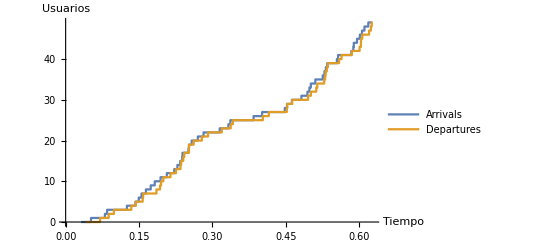

```mathematica
ListStepPlot[{PointStair[ArrivalsTime][[1;;50]],PointStair[DepartuMM2][[1;;50]]}, AxesLabel->{Tiempo, Usuarios}, PlotLegends->{"Arrivals","Departures"}]
```

```mathematica
Manipulate[ListStepPlot[{PointStair[ArrivalsTime][[origin;;origin+width]],PointStair[DepartuMM2][[origin;;origin+width]]}, AxesLabel->{Tiempo, Usuarios}, PlotLegends->{"Arrivals","Departures"}],{origin,1,1000-width,1},{width,10,If[muestras-origin> 0, muestras-origin, 10],1}]
```

```mathematica
ArrivalsEventMM2=CreateEventList[ArrivalsTime, 1];
DepartureEventMM2=CreateEventList[DepartuMM2, -1];
ListaEventosMM2=Sort[Join[ArrivalsEventMM2, DepartureEventMM2]];
usuariosMM2=NumUsers[ListaEventosMM2];
```

Tal y como podemos observar en la siguiente gráfica, el número de usuarios máximos del sistema se ha visto reducido considerablemente. Con una cola M/M/1 teníamos aproximadamente 18, mientras que con una cola M/M/2 tenemos 6. Esto es debido a que al tener 2 servidores, es posible servir dos paquetes en paralelo, reduciendo de esta manera los tiempos de espera del sistema.

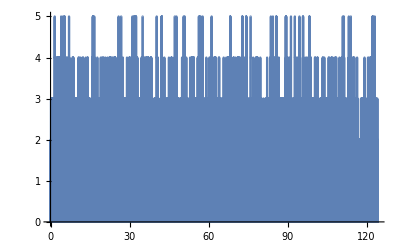

```mathematica
ListLinePlot[usuariosMM2]
```

```mathematica
Manipulate[ListLinePlot[usuariosMM2[[origin;;origin+width]]],{origin,1,Length[usuariosMM2]-width,1},{width,10,If[Length[usuariosMM2]-origin> 0, Length[usuariosMM2]-origin, 10],1}]
```

```mathematica
probPracticaMM2=ProbEstadoPrac[usuariosMM2];
```

A continuación, se puede observar el numero maximo de usuarios para una cola M/M/1 y una cola M/M/2. Tambien se puede observar como se reduce drásticamente el numero maximo en la cola M/M/2.

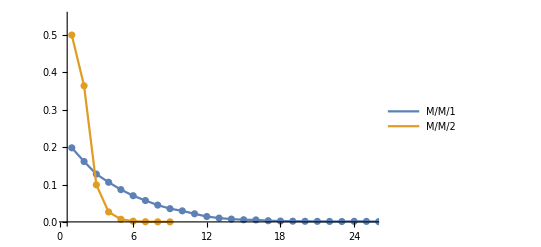

```mathematica
Show[ListPlot[{probPractica, probPracticaMM2}, PlotRange->{{0.5,25.5},{0,0.55}}],ListLinePlot[{probPractica, probPracticaMM2}, {PlotLegends->{"M/M/1","M/M/2"}, PlotRange->{{0.5,25.5},{0,0.55}}}]]
```